### Code

#### Code for sessies

```mathematica
SetDirectory[NotebookDirectory[]];
Needs["SSSiCv100`"];
```

### Tests

Select a ruleset to investigate, possibly by giving its reduced rank index, giving it some convenient name:

```mathematica
rs01=FromReducedRankIndex[253518005]
```

<|Index→253518005,QCode→343233422343,RuleSet→{ABA→AAB,A→ABA}|>

We can pull out the ruleset itself:

```mathematica
rs01[["RuleSet"]]
```

{ABA→AAB,A→ABA}

Or start from a ruleset:

```mathematica
rs02=FromReducedRankRuleSet[{"AA"->"","AB"->"BA","A"->"BB","B"->"AAA"}]
```

<|Index→702927424475,QCode→31342432243424233,RuleSet→{AA→,AB→BA,A→BB,B→AAA}|>

We generate the sessie and its causal network, again giving it a convenient name:

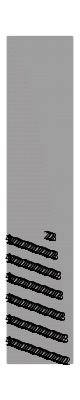


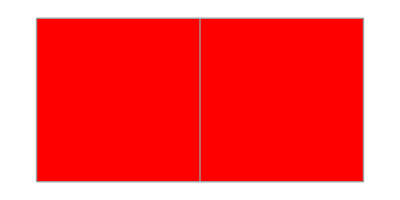

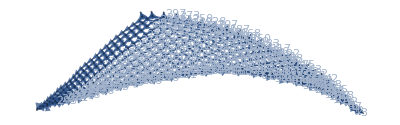
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
sss02=SSS[rs02, "A",400];
```

```mathematica
SSSInteractiveDisplay[sss02]
```

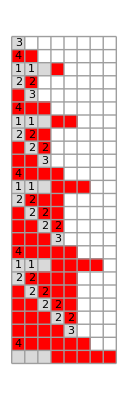
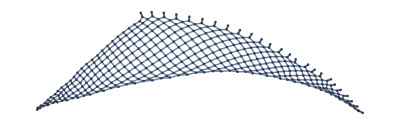
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
SSSDisplay[sss02,Min->1,Max->400,SSSMin->Automatic,SSSMax->25,NetMin->Automatic,NetMax->Automatic,HighlightMethod->Number,RulePlacement->Bottom,NetMethod->{GraphPlot},ImageSize->78.5,NetSize->{Automatic,222.},SSSSize->{Automatic,220},IconSize->{Automatic,20},VertexSize->Automatic,VertexLabels->Placed[Automatic,Tooltip],DirectedEdges->False]
```

```mathematica
SetOptions[SSSDisplay,Min->1,Max->400,SSSMin->Automatic,SSSMax->25,NetMin->Automatic,NetMax->Automatic,HighlightMethod->Number,RulePlacement->Bottom,NetMethod->{GraphPlot},ImageSize->78.5,NetSize->{Automatic,222.},SSSSize->{Automatic,220},IconSize->{Automatic,20},VertexSize->Automatic,VertexLabels->Placed[Automatic,Tooltip],DirectedEdges->False]
```

```mathematica
SSSAnimate[sss02]
```

Then we look at its Net, and create the list of lists of integers that we will summarize:

```mathematica
sss02[["Net"]]//Short
```

{1→2,2→3,2→3,2→4,1→4,4→5,«737»,397→398,372→398,398→399,373→399,399→400,373→400}

```mathematica
SSSInteractiveDisplay[sss02]
```

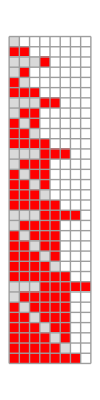
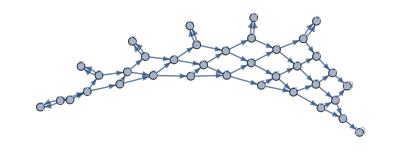
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:
-Graphics--Graphics-

```mathematica
SSSDisplay[sss02,Min->1,Max->400,SSSMin->Automatic,SSSMax->32,NetMin->Automatic,NetMax->36,HighlightMethod->None,RulePlacement->Top,NetMethod->{GraphPlot},ImageSize->119.,NetSize->{Automatic,184.},SSSSize->{Automatic,269.},IconSize->{Automatic,17.05},VertexSize->0.8,VertexLabels->Placed["VertexWeight",Center],DirectedEdges->True]
```

```mathematica
sss02[["Net"]]//Short
```

{1→2,2→3,2→3,2→4,1→4,4→5,4→6,«736»,397→398,372→398,398→399,373→399,399→400,373→400}

```mathematica
nds02=ToNetDifferenceSets[sss02[["Net"]]]
```

{{1,3},{1,1,2},{},{1,2},{3,4},{1,1,2},{},{1,3},{1,4},{4,5},{1,1,2},{},{1,4},{1,5},{1,5},{5,6},{1,1,2},{},{1,5},{1,6},{1,6},{1,6},{6,7},{1,1,2},{},{1,6},{1,7},{1,7},{1,7},{1,7},{7,8},{1,1,2},{},{1,7},{1,8},{1,8},{1,8},{1,8},{1,8},{8,9},{1,1,2},{},{1,8},{1,9},{1,9},{1,9},{1,9},{1,9},{1,9},{9,10},{1,1,2},{},{1,9},{1,10},{1,10},{1,10},{1,10},{1,10},{1,10},{1,10},{10,11},{1,1,2},{},{1,10},{1,11},{1,11},{1,11},{1,11},{1,11},{1,11},{1,11},{1,11},{11,12},{1,1,2},{},{1,11},{1,12},{1,12},{1,12},{1,12},{1,12},{1,12},{1,12},{1,12},{1,12},{12,13},{1,1,2},{},{1,12},{1,13},{1,13},{1,13},{1,13},{1,13},{1,13},{1,13},{1,13},{1,13},{1,13},{13,14},{1,1,2},{},{1,13},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{14,15},{1,1,2},{},{1,14},{1,15},{1,15},{1,15},{1,15},{1,15},{1,15},{1,15},{1,15},{1,15},{1,15},{1,15},{1,15},{15,16},{1,1,2},{},{1,15},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{16,17},{1,1,2},{},{1,16},{1,17},{1,17},{1,17},{1,17},{1,17},{1,17},{1,17},{1,17},{1,17},{1,17},{1,17},{1,17},{1,17},{1,17},{17,18},{1,1,2},{},{1,17},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{18,19},{1,1,2},{},{1,18},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{19,20},{1,1,2},{},{1,19},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{20,21},{1,1,2},{},{1,20},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{21,22},{1,1,2},{},{1,21},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{22,23},{1,1,2},{},{1,22},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{23,24},{1,1,2},{},{1,23},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{24,25},{1,1,2},{},{1,24},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{25,26},{1,1,2},{},{1,25},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{26,27},{1,1,2},{},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1}}

```mathematica
rsl02=ReduceSetList[nds02]
```

{{1,3},{1,1,2},{},{1,2},{3,4},{1,1,2},{},€_(n$1⊨1)^2[{1,2+n$1}],€_(n$2⊨1)^22[{3+n$2,4+n$2},{1,1,2},{},{1,3+n$2},€^(1+n$2)[{1,4+n$2}]],{26,27},{1,1,2},{},€^24[{1}]}

You may need to limit the part of the nds list that you try to compact, omitting the incomplete sets at the end of the list. In theory it’s not needed to start later than the beginning of the list.  In this case the most compact part is what we want:

```mathematica
rsl02[[9]]
```

€_(n$2⊨1)^22[{3+n$2,4+n$2},{1,1,2},{},{1,3+n$2},€^(1+n$2)[{1,4+n$2}]]

If that doesn’t work, you can figure out a place to stop:

```mathematica
Position[nds02,27]
```

{{373,2}}

```mathematica
nds02[[1;;372]]
```

{{1,3},{1,1,2},{},{1,2},{3,4},{1,1,2},{},{1,3},{1,4},{4,5},{1,1,2},{},{1,4},{1,5},{1,5},{5,6},{1,1,2},{},{1,5},{1,6},{1,6},{1,6},{6,7},{1,1,2},{},{1,6},{1,7},{1,7},{1,7},{1,7},{7,8},{1,1,2},{},{1,7},{1,8},{1,8},{1,8},{1,8},{1,8},{8,9},{1,1,2},{},{1,8},{1,9},{1,9},{1,9},{1,9},{1,9},{1,9},{9,10},{1,1,2},{},{1,9},{1,10},{1,10},{1,10},{1,10},{1,10},{1,10},{1,10},{10,11},{1,1,2},{},{1,10},{1,11},{1,11},{1,11},{1,11},{1,11},{1,11},{1,11},{1,11},{11,12},{1,1,2},{},{1,11},{1,12},{1,12},{1,12},{1,12},{1,12},{1,12},{1,12},{1,12},{1,12},{12,13},{1,1,2},{},{1,12},{1,13},{1,13},{1,13},{1,13},{1,13},{1,13},{1,13},{1,13},{1,13},{1,13},{13,14},{1,1,2},{},{1,13},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{14,15},{1,1,2},{},{1,14},{1,15},{1,15},{1,15},{1,15},{1,15},{1,15},{1,15},{1,15},{1,15},{1,15},{1,15},{1,15},{15,16},{1,1,2},{},{1,15},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{16,17},{1,1,2},{},{1,16},{1,17},{1,17},{1,17},{1,17},{1,17},{1,17},{1,17},{1,17},{1,17},{1,17},{1,17},{1,17},{1,17},{1,17},{17,18},{1,1,2},{},{1,17},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{18,19},{1,1,2},{},{1,18},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{19,20},{1,1,2},{},{1,19},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{20,21},{1,1,2},{},{1,20},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{21,22},{1,1,2},{},{1,21},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{22,23},{1,1,2},{},{1,22},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{23,24},{1,1,2},{},{1,23},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{24,25},{1,1,2},{},{1,24},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{25,26},{1,1,2},{},{1,25},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26}}

Try the reduction again:

```mathematica
rsl02=ReduceSetList[nds02[[1;;372]]]
```

{{1,3},{1,1,2},{},{1,2},{3,4},{1,1,2},{},€_(n$1⊨1)^2[{1,2+n$1}],€_(n$2⊨1)^22[{3+n$2,4+n$2},{1,1,2},{},{1,3+n$2},€^(1+n$2)[{1,4+n$2}]]}

The most compressed part is

```mathematica
rsl02[[9]]/.n$2->k
```

€_(k⊨1)^22[{3+k,4+k},{1,1,2},{},{1,3+k},€^(1+k)[{1,4+k}]]

```mathematica
rsl02[[9]]/.n$2->k//InputForm
```

```mathematica
IndexedConcatenate[{3 + k, 4 + k}, {1, 1, 2}, {}, {1, 3 + k}, 
 IndexedConcatenate[{1, 4 + k}, 1 + k], {k, -2, 12}]
```

€_(k⊨-2)^12[{k+3,k+4},{1,1,2},{},{1,k+3},€^(k+1)[{1,k+4}]]

Start it earlier, stop it whenever you want.

This is the same thing as

```mathematica
IndexedConcatenate[{n$2, n$2+1}, {1, 1, 2}, {}, {1, n$2}, IndexedConcatenate[{1, n$2+1}, n$2-2], {n$2, 1, 15}]/.n$2->k
```

€_(k⊨1)^15[{k,k+1},{1,1,2},{},{1,k},€^(k-2)[{1,k+1}]]

```mathematica
{ExpandAll[%]}
```

{{1,2},{1,1,2},{},{1,1},{2,3},{1,1,2},{},{1,2},{3,4},{1,1,2},{},{1,3},{1,4},{4,5},{1,1,2},{},{1,4},{1,5},{1,5},{5,6},{1,1,2},{},{1,5},{1,6},{1,6},{1,6},{6,7},{1,1,2},{},{1,6},{1,7},{1,7},{1,7},{1,7},{7,8},{1,1,2},{},{1,7},{1,8},{1,8},{1,8},{1,8},{1,8},{8,9},{1,1,2},{},{1,8},{1,9},{1,9},{1,9},{1,9},{1,9},{1,9},{9,10},{1,1,2},{},{1,9},{1,10},{1,10},{1,10},{1,10},{1,10},{1,10},{1,10},{10,11},{1,1,2},{},{1,10},{1,11},{1,11},{1,11},{1,11},{1,11},{1,11},{1,11},{1,11},{11,12},{1,1,2},{},{1,11},{1,12},{1,12},{1,12},{1,12},{1,12},{1,12},{1,12},{1,12},{1,12},{12,13},{1,1,2},{},{1,12},{1,13},{1,13},{1,13},{1,13},{1,13},{1,13},{1,13},{1,13},{1,13},{1,13},{13,14},{1,1,2},{},{1,13},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{14,15},{1,1,2},{},{1,14},{1,15},{1,15},{1,15},{1,15},{1,15},{1,15},{1,15},{1,15},{1,15},{1,15},{1,15},{1,15},{15,16},{1,1,2},{},{1,15},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16}}

```mathematica
GraphPlot[FromNetDifferenceSets@%]
```

-Graphics-

#### Two Linear (1D) examples

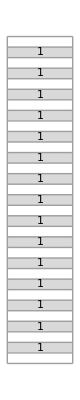
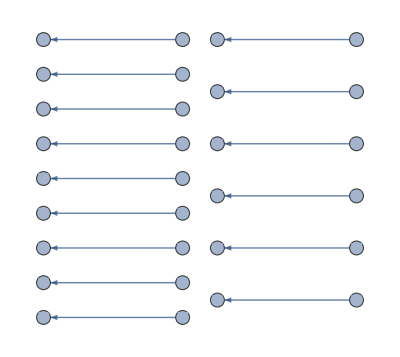
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
ssslin1=SSS[FromReducedRankIndex[2],"",30];
```

```mathematica
ssslin1[["Net"]]
```

{1→2,3→4,5→6,7→8,9→10,11→12,13→14,15→16,17→18,19→20,21→22,23→24,25→26,27→28,29→30}

```mathematica
ToNetDifferenceSets[ssslin1[["Net"]]]
```

{{1},{},{1},{},{1},{},{1},{},{1},{},{1},{},{1},{},{1},{},{1},{},{1},{},{1},{},{1},{},{1},{},{1},{},{1}}

```mathematica
ReduceSetList@%
```

{€^14[{1},{}],{1}}

Use most compact part:

```mathematica
{€^14[{1},{}]}
```

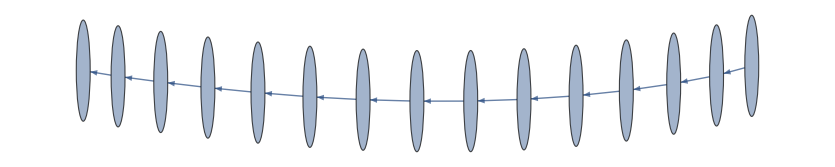
-Graphics-
-Graphics- | → | -Graphics-Substitution Rule:-Graphics-

```mathematica
ssslin2=SSS[FromReducedRankIndex[4],"A",15,NetSize->550];
```

```mathematica
ssslin2[["Net"]]
```

{1→2,2→3,3→4,4→5,5→6,6→7,7→8,8→9,9→10,10→11,11→12,12→13,13→14,14→15}

```mathematica
ToNetDifferenceSets[ssslin2[["Net"]]]
```

{{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1}}

```mathematica
ReduceSetList@%
```

{€^14[{1}]}

Note: pull up Jeanna Toulouse’s & Chris Trana’s posters, compare to their network summaries!

#### The 2D (mostly) hexagonal network

```mathematica
rsHex=FromReducedRankRuleSet[{"AA"->"BA","AB"->"AA","B"->"AA"}]
```

<|Index→1181262395,QCode→3243234232423,RuleSet→{AA→BA,AB→AA,B→AA}|>

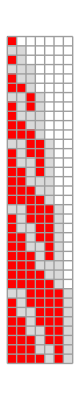
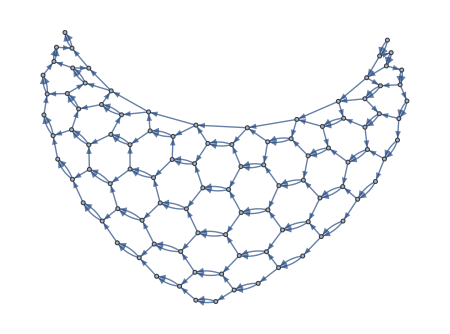
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules: | -Graphics--Graphics-

```mathematica
sssHex=SSS[rsHex, "B",400, (* choose an appropriate initial state string, and # steps *)
(* options *) SSSMax->35,NetMax->100,NetSize->{450,Automatic},SSSSize->{Automatic,320},HighlightMethod->None,RulePlacement->Left,VertexLabels->Placed[Automatic,Tooltip],DirectedEdges->True,ImageSize->304.,NetSize->{Automatic,338.},SSSSize->{Automatic,486.},IconSize->{Automatic,31.8},VertexSize->Automatic];
```

```mathematica
sssHex["Distance"]
```

{0,1,2,3,2,4,5,3,4,3,6,7,5,6,4,5,4,8,9,7,8,6,7,5,6,5,10,11,9,10,8,9,7,8,6,7,6,12,13,11,12,10,11,9,10,8,9,7,8,7,14,15,13,14,12,13,11,12,10,11,9,10,8,9,8,16,17,15,16,14,15,13,14,12,13,11,12,10,11,9,10,9,18,19,17,18,16,17,15,16,14,15,13,14,12,13,11,12,10,11,10,20,21,19,20,18,19,17,18,16,17,15,16,14,15,13,14,12,13,11,12,11,22,23,21,22,20,21,19,20,18,19,17,18,16,17,15,16,14,15,13,14,12,13,12,24,25,23,24,22,23,21,22,20,21,19,20,18,19,17,18,16,17,15,16,14,15,13,14,13,26,27,25,26,24,25,23,24,22,23,21,22,20,21,19,20,18,19,17,18,16,17,15,16,14,15,14,28,29,27,28,26,27,25,26,24,25,23,24,22,23,21,22,20,21,19,20,18,19,17,18,16,17,15,16,15,30,31,29,30,28,29,27,28,26,27,25,26,24,25,23,24,22,23,21,22,20,21,19,20,18,19,17,18,16,17,16,32,33,31,32,30,31,29,30,28,29,27,28,26,27,25,26,24,25,23,24,22,23,21,22,20,21,19,20,18,19,17,18,17,34,35,33,34,32,33,31,32,30,31,29,30,28,29,27,28,26,27,25,26,24,25,23,24,22,23,21,22,20,21,19,20,18,19,18,36,37,35,36,34,35,33,34,32,33,31,32,30,31,29,30,28,29,27,28,26,27,25,26,24,25,23,24,22,23,21,22,20,21,19,20,19,38,39,37,38,36,37,35,36,34,35,33,34,32,33,31,32,30,31,29,30,28,29,27,28,26,27,25,26,24,25,23,24,22,23,21,22,20,21}

```mathematica
Tally[sssHex["Distance"]]
```

{{0,1},{1,1},{2,2},{3,3},{4,4},{5,5},{6,6},{7,7},{8,8},{9,9},{10,10},{11,11},{12,12},{13,13},{14,14},{15,15},{16,16},{17,17},{18,18},{19,19},{20,19},{21,19},{22,18},{23,17},{24,16},{25,15},{26,14},{27,13},{28,12},{29,11},{30,10},{31,9},{32,8},{33,7},{34,6},{35,5},{36,4},{37,3},{38,2},{39,1}}

```mathematica
Tally[sssHex["Distance"]][[1;;20]]
```

{{0,1},{1,1},{2,2},{3,3},{4,4},{5,5},{6,6},{7,7},{8,8},{9,9},{10,10},{11,11},{12,12},{13,13},{14,14},{15,15},{16,16},{17,17},{18,18},{19,19}}

```mathematica
Last/@%140
```

{1,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19}

```mathematica
Accumulate[%]
```

{1,2,4,7,11,16,22,29,37,46,56,67,79,92,106,121,137,154,172,191}

```mathematica
NestList[Differences,%,2]//Grid
```

1 | 2 | 4 | 7 | 11 | 16 | 22 | 29 | 37 | 46 | 56 | 67 | 79 | 92 | 106 | 121 | 137 | 154 | 172 | 191
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  |

```mathematica
sssHex["Net"]//Short
```

{1→2,1→2,2→3,3→4,3→4,4→5,2→5,«766»,397→398,397→398,398→399,362→399,399→400,399→400}

```mathematica
ToNetDifferenceSets[sssHex["Net"]]
```

{{1,1},{1,3},{1,1},{1,2},{3,5},{1,1},{1,4},{1,1},{1,4},{5,7},{1,1},{1,6},{1,1},{1,6},{1,1},{1,6},{7,9},{1,1},{1,8},{1,1},{1,8},{1,1},{1,8},{1,1},{1,8},{9,11},{1,1},{1,10},{1,1},{1,10},{1,1},{1,10},{1,1},{1,10},{1,1},{1,10},{11,13},{1,1},{1,12},{1,1},{1,12},{1,1},{1,12},{1,1},{1,12},{1,1},{1,12},{1,1},{1,12},{13,15},{1,1},{1,14},{1,1},{1,14},{1,1},{1,14},{1,1},{1,14},{1,1},{1,14},{1,1},{1,14},{1,1},{1,14},{15,17},{1,1},{1,16},{1,1},{1,16},{1,1},{1,16},{1,1},{1,16},{1,1},{1,16},{1,1},{1,16},{1,1},{1,16},{1,1},{1,16},{17,19},{1,1},{1,18},{1,1},{1,18},{1,1},{1,18},{1,1},{1,18},{1,1},{1,18},{1,1},{1,18},{1,1},{1,18},{1,1},{1,18},{1,1},{1,18},{19,21},{1,1},{1,20},{1,1},{1,20},{1,1},{1,20},{1,1},{1,20},{1,1},{1,20},{1,1},{1,20},{1,1},{1,20},{1,1},{1,20},{1,1},{1,20},{1,1},{1,20},{21,23},{1,1},{1,22},{1,1},{1,22},{1,1},{1,22},{1,1},{1,22},{1,1},{1,22},{1,1},{1,22},{1,1},{1,22},{1,1},{1,22},{1,1},{1,22},{1,1},{1,22},{1,1},{1,22},{23,25},{1,1},{1,24},{1,1},{1,24},{1,1},{1,24},{1,1},{1,24},{1,1},{1,24},{1,1},{1,24},{1,1},{1,24},{1,1},{1,24},{1,1},{1,24},{1,1},{1,24},{1,1},{1,24},{1,1},{1,24},{25,27},{1,1},{1,26},{1,1},{1,26},{1,1},{1,26},{1,1},{1,26},{1,1},{1,26},{1,1},{1,26},{1,1},{1,26},{1,1},{1,26},{1,1},{1,26},{1,1},{1,26},{1,1},{1,26},{1,1},{1,26},{1,1},{1,26},{27,29},{1,1},{1,28},{1,1},{1,28},{1,1},{1,28},{1,1},{1,28},{1,1},{1,28},{1,1},{1,28},{1,1},{1,28},{1,1},{1,28},{1,1},{1,28},{1,1},{1,28},{1,1},{1,28},{1,1},{1,28},{1,1},{1,28},{1,1},{1,28},{29,31},{1,1},{1,30},{1,1},{1,30},{1,1},{1,30},{1,1},{1,30},{1,1},{1,30},{1,1},{1,30},{1,1},{1,30},{1,1},{1,30},{1,1},{1,30},{1,1},{1,30},{1,1},{1,30},{1,1},{1,30},{1,1},{1,30},{1,1},{1,30},{1,1},{1,30},{31,33},{1,1},{1,32},{1,1},{1,32},{1,1},{1,32},{1,1},{1,32},{1,1},{1,32},{1,1},{1,32},{1,1},{1,32},{1,1},{1,32},{1,1},{1,32},{1,1},{1,32},{1,1},{1,32},{1,1},{1,32},{1,1},{1,32},{1,1},{1,32},{1,1},{1,32},{1,1},{1,32},{33,35},{1,1},{1,34},{1,1},{1,34},{1,1},{1,34},{1,1},{1,34},{1,1},{1,34},{1,1},{1,34},{1,1},{1,34},{1,1},{1,34},{1,1},{1,34},{1,1},{1,34},{1,1},{1,34},{1,1},{1,34},{1,1},{1,34},{1,1},{1,34},{1,1},{1,34},{1,1},{1,34},{1,1},{1,34},{35,37},{1,1},{1,36},{1,1},{1,36},{1,1},{1,36},{1,1},{1,36},{1,1},{1,36},{1,1},{1,36},{1,1},{1,36},{1,1},{1,36},{1,1},{1,36},{1,1},{1,36},{1,1},{1,36},{1,1},{1,36},{1,1},{1,36},{1,1},{1,36},{1,1},{1,36},{1,1},{1,36},{1,1},{1,36},{1,1},{1,36},{37},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1}}

```mathematica
ReduceSetList[%34]
```

{€_(n$1⊨1)^2[{1,1},{1,4-n$1}],€_(n$1⊨1)^17[{1+2 n$1,3+2 n$1},€^(1+n$1)[{1,1},{1,2 (1+n$1)}]],{37},€^18[{1,1},{1}],{1,1}}

```mathematica
Position[%,37]
```

{{325,2},{362,1}}

```mathematica
%150[[1;;362]]
```

{{1,1},{1,3},{1,1},{1,2},{3,5},{1,1},{1,4},{1,1},{1,4},{5,7},{1,1},{1,6},{1,1},{1,6},{1,1},{1,6},{7,9},{1,1},{1,8},{1,1},{1,8},{1,1},{1,8},{1,1},{1,8},{9,11},{1,1},{1,10},{1,1},{1,10},{1,1},{1,10},{1,1},{1,10},{1,1},{1,10},{11,13},{1,1},{1,12},{1,1},{1,12},{1,1},{1,12},{1,1},{1,12},{1,1},{1,12},{1,1},{1,12},{13,15},{1,1},{1,14},{1,1},{1,14},{1,1},{1,14},{1,1},{1,14},{1,1},{1,14},{1,1},{1,14},{1,1},{1,14},{15,17},{1,1},{1,16},{1,1},{1,16},{1,1},{1,16},{1,1},{1,16},{1,1},{1,16},{1,1},{1,16},{1,1},{1,16},{1,1},{1,16},{17,19},{1,1},{1,18},{1,1},{1,18},{1,1},{1,18},{1,1},{1,18},{1,1},{1,18},{1,1},{1,18},{1,1},{1,18},{1,1},{1,18},{1,1},{1,18},{19,21},{1,1},{1,20},{1,1},{1,20},{1,1},{1,20},{1,1},{1,20},{1,1},{1,20},{1,1},{1,20},{1,1},{1,20},{1,1},{1,20},{1,1},{1,20},{1,1},{1,20},{21,23},{1,1},{1,22},{1,1},{1,22},{1,1},{1,22},{1,1},{1,22},{1,1},{1,22},{1,1},{1,22},{1,1},{1,22},{1,1},{1,22},{1,1},{1,22},{1,1},{1,22},{1,1},{1,22},{23,25},{1,1},{1,24},{1,1},{1,24},{1,1},{1,24},{1,1},{1,24},{1,1},{1,24},{1,1},{1,24},{1,1},{1,24},{1,1},{1,24},{1,1},{1,24},{1,1},{1,24},{1,1},{1,24},{1,1},{1,24},{25,27},{1,1},{1,26},{1,1},{1,26},{1,1},{1,26},{1,1},{1,26},{1,1},{1,26},{1,1},{1,26},{1,1},{1,26},{1,1},{1,26},{1,1},{1,26},{1,1},{1,26},{1,1},{1,26},{1,1},{1,26},{1,1},{1,26},{27,29},{1,1},{1,28},{1,1},{1,28},{1,1},{1,28},{1,1},{1,28},{1,1},{1,28},{1,1},{1,28},{1,1},{1,28},{1,1},{1,28},{1,1},{1,28},{1,1},{1,28},{1,1},{1,28},{1,1},{1,28},{1,1},{1,28},{1,1},{1,28},{29,31},{1,1},{1,30},{1,1},{1,30},{1,1},{1,30},{1,1},{1,30},{1,1},{1,30},{1,1},{1,30},{1,1},{1,30},{1,1},{1,30},{1,1},{1,30},{1,1},{1,30},{1,1},{1,30},{1,1},{1,30},{1,1},{1,30},{1,1},{1,30},{1,1},{1,30},{31,33},{1,1},{1,32},{1,1},{1,32},{1,1},{1,32},{1,1},{1,32},{1,1},{1,32},{1,1},{1,32},{1,1},{1,32},{1,1},{1,32},{1,1},{1,32},{1,1},{1,32},{1,1},{1,32},{1,1},{1,32},{1,1},{1,32},{1,1},{1,32},{1,1},{1,32},{1,1},{1,32},{33,35},{1,1},{1,34},{1,1},{1,34},{1,1},{1,34},{1,1},{1,34},{1,1},{1,34},{1,1},{1,34},{1,1},{1,34},{1,1},{1,34},{1,1},{1,34},{1,1},{1,34},{1,1},{1,34},{1,1},{1,34},{1,1},{1,34},{1,1},{1,34},{1,1},{1,34},{1,1},{1,34},{1,1},{1,34},{35,37},{1,1},{1,36},{1,1},{1,36},{1,1},{1,36},{1,1},{1,36},{1,1},{1,36},{1,1},{1,36},{1,1},{1,36},{1,1},{1,36},{1,1},{1,36},{1,1},{1,36},{1,1},{1,36},{1,1},{1,36},{1,1},{1,36},{1,1},{1,36},{1,1},{1,36},{1,1},{1,36},{1,1},{1,36},{1,1},{1,36},{37}}

```mathematica
ReduceSetList[%152]
```

{€_(n$1⊨1)^2[{1,1},{1,4-n$1}],€_(n$1⊨1)^17[{2 n$1+1,2 n$1+3},€^(n$1+1)[{1,1},{1,2 (n$1+1)}]],{37}}

```mathematica
%153[[2]]/.n$1->k//InputForm
```

```mathematica
IndexedConcatenate[{1 + 2*k, 3 + 2*k}, IndexedConcatenate[{1, 1}, {1, 2*(1 + k)}, 1 + k], {k, 1, 17}]
```

€_(k⊨1)^17[{2 k+1,2 k+3},€^(k+1)[{1,1},{1,2 (k+1)}]]

```mathematica
IndexedConcatenate[{1 + 2 k, 3 + 2 k}, IndexedConcatenate[{1, 1}, {1, 2*(1 + k)}, 1 + k], {k, 0, 16}]
```

€_(k⊨0)^16[{2 k+1,2 k+3},€^(k+1)[{1,1},{1,2 (k+1)}]]

```mathematica
IndexedConcatenate[{-1 + 2 k, 1 + 2 k}, IndexedConcatenate[{1, 1}, {1, 2 k}, k], {k, 1, 17}]
```

€_(k⊨1)^17[{2 k-1,2 k+1},€^k[{1,1},{1,2 k}]]

```mathematica
{ExpandAll[%173]}=={ExpandAll[%176]}
```

True